# Extending SML Package - Hierarchical Solver for the Stationary Distribution on the boundaries of a Markov One-step Process

## Method

## Functions

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
Needs["CCompilerDriver`"];
If[Length[CCompilers[]]==0,
$CCompiler={"Name"->"Intel Compiler","Compiler"->CCompilerDriver`IntelCompiler`IntelCompiler,"CompilerInstallation"->"D:\\Program Files (x86)\\Intel\\Composer XE 2015","CompilerName"->Automatic};
];
DiscreteZero=Compile[{{vecXY,_Real,2}},
Module[{
dx=Internal`Bag[Most[{0.}]],
x=Internal`Bag[Most[{0.}]],
index=Internal`Bag[Most[{0}]],
Z=Length[vecXY]-1,
xtemp=0.,
dxtemp=0.,
thereAreZeros=False
},

Do[
If[vecXY[[i,2]]>= 0&&vecXY[[i+1,2]]< 0,
If[vecXY[[i,2]]== 0&&i>1,
Internal`StuffBag[dx,(vecXY[[i+1,2]]-If[i>1,vecXY[[i-1,2]],vecXY[[i,2]]])/(vecXY[[i+1,1]]-If[i>1,vecXY[[i-1,1]],vecXY[[i,1]]])];
Internal`StuffBag[x,vecXY[[i,1]]];
Internal`StuffBag[index,i];
If[!thereAreZeros,thereAreZeros=True;];
,
dxtemp=(vecXY[[i+1,2]]-vecXY[[i,2]])/(vecXY[[i+1,1]]-vecXY[[i,1]]);
xtemp=vecXY[[i,1]]-vecXY[[i,2]]/((vecXY[[i+1,2]]-vecXY[[i,2]])/(vecXY[[i+1,1]]-vecXY[[i,1]])); 

If[Abs[xtemp-vecXY[[i,1]]]<Abs[xtemp-vecXY[[i+1,1]]]&&i>1,
Internal`StuffBag[dx,dxtemp];
Internal`StuffBag[x,xtemp];
Internal`StuffBag[index,i];
If[!thereAreZeros,thereAreZeros=True;];
,
If[i>1&&i<Z,
Internal`StuffBag[dx,dxtemp];
Internal`StuffBag[x,xtemp];
Internal`StuffBag[index,i+1];
If[!thereAreZeros,thereAreZeros=True;];
];
];];
];
,{i,1,Z}];



If[thereAreZeros,
Transpose[{Internal`BagPart[dx,All,List],Internal`BagPart[x,All,List],Internal`BagPart[index,All,List]}],
{{}}
]
]
,CompilationTarget->"C"];
```

```mathematica
DiscreteZero[Transpose@{Range[0,3]/3,{0.2,0.55,0.4,0.1}-{0.1,0.5,0.35,0.2}}]
```

{{-0.45,0.777778,3.}}

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
TransitionsPairs::difdimensions="The lenght of the first list, `1`, is equal to that of the second, `2`.";
TransitionsPairs[Tp_List,Tm_List]:=If[Length[Tp]==Length[Tm],With[{Z=Length[Tp]-1},
Module[{zeros=DiscreteZero[Transpose@{Range[0,Z]/Z,Tp-Tm}], CoIindex={1,Z+1},Pp=1.,Pm=1.},

If[zeros≠{{}},
CoIindex=Flatten@Insert[CoIindex,IntegerPart[zeros[[All,-1]]],2] ;


{Transpose@{
CoIindex, (* Point index, from 1 to Z+1 *)
Flatten[{0.,zeros[[All,2]],1.}],(*Point position from 0 to 1*)
Flatten[{1.,zeros[[All,1]],1.}],(*Drift derivative*)
Flatten[{1.,Table[(Tm[[CoIindex[[i]]]]+Tp[[CoIindex[[i]]]])/(2Z),{i,2,Length[CoIindex]-1}],1.}](*Diffusion*)
},
SparseArray[Flatten[Table[

(*Pp=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tm[[k]]/Tp[[k]];*)
Pp=1.;Do[Pp=1.+Pp Tm[[k]]/Tp[[k]];,{k,CoIindex[[i]]+1,CoIindex[[i+1]]-1}];
(*Pm=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tp[[k]]/Tm[[k]]*)
Pm=1.;Do[Pm=1.+Pm Tp[[k]]/Tm[[k]];,{k,CoIindex[[i+1]]-1,CoIindex[[i]]+1,-1}];
(*CoI[[i]] to CoI[[i+1]]  and   CoI[[i+1]] to CoI[[i]]*)

{{i,i+1}-> Tp[[CoIindex[[i]]]]/Pp,{i+1,i}->Tm[[CoIindex[[i+1]]]]/Pm}
,{i,1,Length[CoIindex]-1}]],{Length[CoIindex],Length[CoIindex]}]
},


{Transpose@{
CoIindex, (* Point index, from 1 to Z+1 *)
{0.,1.},(*Point position from 0 to 1*)
{1.,1.},(*Drift derivative*)
{1.,1.}(*Diffusion*)
},
SparseArray[

(*Pp=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tm[[k]]/Tp[[k]];*)
Pp=1.;Do[Pp=1.+Pp Tm[[k]]/Tp[[k]];,{k,2,Z}];
(*Pm=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tp[[k]]/Tm[[k]]*)
Pm=1.;Do[Pm=1.+Pm Tp[[k]]/Tm[[k]];,{k,Z,2,-1}];
(*CoI[[i]] to CoI[[i+1]]  and   CoI[[i+1]] to CoI[[i]]*)

{{1,2}-> Tp[[1]]/Pp,{2,1}->Tm[[Z+1]]/Pm}
,{Length[CoIindex],Length[CoIindex]}]
}


]

]]
,Message[TransitionsPairs::difdimensions,Dimensions[Tp],Dimensions[Tm]]];
```

```mathematica
TransitionsPairs[{0.2,0.55,0.4,0.1},{0.1,0.5,0.35,0.0}]
```

{{{1,0.,1.,1.},{4,1.,1.,1.}},SparseArray[<1>, {2, 2}]}

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
TransitionMatrixESML::usage="TransitionMatrixESML[s,T,Z,{par1,par2...}] represents the transition matrix between a set of Configurations of Interest (CoI) in the long run of a one-step Markov process at the edges of the phase space (first order approximation) as well as the set itself. The process is i=(i_1,...,i_s) such that ∑_(k = 1)^s i_k=Z and T[fs,ts,k,Z,{par1,par2...}] is the transition probability from configuration (0,...,i_fs=k,...,i_ts=Z-k,...,0) to (0,...,i_fs=k-1,...,i_ts=Z-k+1,...,0) in each time step. The output is of the form {CoI, TransitionMatrix}, where TransitionMatrix is a sparse array and CoI contains a list {{CoI_1,DDrift_1,diffusion_1}, ...,} where CoI_i is an array {i_1,...,i_s} with the position of the CoI, DDrift_i and diffusion_i are, respectively, the derivative of the drift (1st Kramers-Moyal term) and the diffusion (2nd Kramers-Moyal term) at the CoI.\n

TransitionMatrixESML[s,T,Z,{par1,par2...},export] allows to export the transition matrix to a file TransitionMatrix_par1_par2_....mtx and the CoI to a file ConfigurationsOfInterest_par1_par2_....mx that can be imported latter on (the .mx file is not OS or architechture independent).";


TransitionMatrixESML::transitiondefinition="The function `1` is undefined. Please guarantee that `1`[s1,s2,i,`2`,`3`] has definition.";
TransitionMatrixESML[s_,T_,Z_,par_List, export_:False]:=If[ValueQ[T[2,1,0,Z,par]],
With[{prints=False},
Module[{CoIFull={{0}},innerCoI={{0.}},ρTemp={{0}},ρ={{0}},pairId=0,zeros={{0.,0.,0}},TMat,speed={0.},innerCoIcount=0,
CoI=Table[{SparseArray[{i->Z},{s}],1.,1.},{i,1,s}],temp
},



(*****************************************************************************)
If[prints,temp=PrintTemporary["Computing CoI and Transitions"];];
(*****************************************************************************)
{innerCoI,ρ}=Rest[Reap[

Do[pairId++;

{zeros,ρTemp}=TransitionsPairs[Table[T[s2,s1,Z-i,Z,par],{i,0,Z}],Table[T[s1,s2,i,Z,par],{i,0,Z}]];

If[Length[zeros]>2,
Sow[Table[{
SparseArray[{s1->(zeros[[i,1]]-1),s2->(Z-(zeros[[i,1]]-1))},{s}],zeros[[i,3]],zeros[[i,4]]}
,{i,2,Length[zeros]-1}],CoIinfo];
,
Sow[{},CoIinfo];
];

Do[

Sow[{Which[array[[1,1]]==1,s2,array[[1,1]]==Length[ρTemp],s1,True,s+innerCoIcount+array[[1,1]]-1],Which[array[[1,2]]==1,s2,array[[1,2]]==Length[ρTemp],s1,True,s+innerCoIcount+array[[1,2]]-1]}->array[[2]],traMat];

,{array,ArrayRules[ρTemp][[1;;-2]]}];

innerCoIcount+=Length[zeros]-2;

,{s1,1,s-1},{s2,s1+1,s}];
]][[1]];

If[prints,NotebookDelete[temp];];
(*****************************************************************************)

innerCoI=Flatten[innerCoI,1];

If[prints,temp=PrintTemporary["Flatten do CoI"];];
CoI=Flatten[{CoI,innerCoI},1];
If[prints,NotebookDelete[temp];];
(*****************************************************************************)
If[prints,temp=PrintTemporary["Matrix construction"];];
(*****************************************************************************)
TMat=SparseArray[ρ,{1,1}(s+innerCoIcount)];

speed=Total[Transpose@TMat];
TMat/=Max[speed];
speed/=Max[speed]; 



If[prints,NotebookDelete[temp];];
(*****************************************************************************)


Do[TMat[[i,i]]=1-speed[[i]];
,{i,1,Length@TMat}];

If[export,
SetDirectory[NotebookDirectory[]];
Export["TransitionMatrix_"<>StringDelete[StringReplace[ToString[par],", "->"_"],{"{","}"}]<>".mtx",TMat];
Export["ConfigurationsOfInterest_"<>StringDelete[StringReplace[ToString[par],", "->"_"],{"{","}"}]<>".mx",CoI];
];

{CoI,TMat}

]
],

Message[StatDESML::transitiondefinition,T,Z,par];
{{{}},{{}}}
];
```

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
StationaryDistributionESML::usage="StationaryDistributionESML[s,Z,ConfigurationsOfInterest,TransitionMatrix] represents an estimation of the stationary distribution of a one-step Markov process at the edges of the phase space. ConfigurationsOfInterest contains a list {{CoI_1,DDrift_1,diffusion_1}, ...,} where CoI_i is an array {i_1,...,i_s} with the position of the Configurations of Interest (CoI), DDrift_i and diffusion_i are, respectively, the derivative of the drift (1st Kramers-Moyal term) and the diffusion (2nd Kramers-Moyal term) at the CoI. The first s elements must be monomorphic configurations (only one non-zero entrance, equal to Z) and any positive value for DDrift ad diffusion at those is valid. TransitionMatrix is a sparse array with the transition probabilities between the CoI in the long run. Both ConfigurationsOfInterest and TransitionMatrix can be obtained from TransitionMatrixESML (see ?TransitionMatrixESML for details).";

StationaryDistributionESML::transitiondefinition="The function `1` is undefined. Please guarantee that `1`[s1,s2,i,`2`,`3`] has definition.";
StationaryDistributionESML[s_,Z_,CoI_,TMat_,initVec_:Automatic]:=
With[{prints=False},
Module[{ vec={0.},speed={0.},temp},

vec=Eigenvectors[Transpose@TMat,1,Method->{"Arnoldi","Shift"->1.00001,"Tolerance"-> 0,"MaxIterations"->10^4,"StartingVector"->initVec}];

(*****************************************************************************)
If[prints,temp=PrintTemporary["Renormalization"];];
(*****************************************************************************)
Which[
Length[vec]==0,
Print["Could not compute Stationary Distribution."];
vec=ConstantArray[0,Length@CoI];
,
Length[vec]>1,
Print["Stationary Distribution was computed but might contain errors."];
vec=vec[[-1]];
,
True,
vec=vec[[1]];

Do[
If[CoI[[i,2]]<0,vec[[i]]*=Z √(2π CoI[[i,3]]/(-CoI[[i,2]]))];
,{i,s+1,Length@vec}];

vec=vec/Total[vec];

];

If[prints,NotebookDelete[temp];];


{CoI[[All,1]],vec}


]
];
```

## Using the function

lalala game theory

```mathematica
<<"ESMLPack`"
```

```mathematica
Δf[i_,Z_,is_,β_]:=β(i-is)/Z;
Tp[i_,Z_,is_,β_,μ_]:=(Z-i)/Z(i/(Z-1)1/(1+ⅇ^(-Δf[i,Z,is,β]))(1-μ)+μ);
Tm[i_,Z_,is_,β_,μ_]:=i/Z((Z-i)/(Z-1)1/(1+ⅇ^Δf[i,Z,is,β])(1-μ)+μ);
T12[i_,Z_,is_,β_,μ_]:=i/Z((Z-i)/(Z-1)1/(1+ⅇ^Δf[i,Z,is,β])(1-μ)+μ);
T21[i_,Z_,is_,β_,μ_]:=i/Z((Z-i)/(Z-1)1/(1+ⅇ^(-Δf[Z-i,Z,is,β]))(1-μ)+μ);
T[fs_,ts_,k_,Z_,par_List]:=Module[{β=par[[1]],μ=par[[2]],is=par[[3]]},
If[fs==1&&ts==2,
T12[k,Z,is,β,μ],
If[fs==2&&ts==1,
T21[k,Z,is,β,μ],
If[fs==1&&ts==3,
T12[k,Z,is,β,μ],
If[fs==3&&ts==1,
T21[k,Z,is,β,μ],
If[fs==2&&ts==3,
T12[k,Z,is,β,μ],
If[fs==3&&ts==2,
T21[k,Z,is,β,μ],
"error"
]]]]]]];
```

```mathematica
plotA=With[{Z=50,β=-10.,is=35},
Module[{CoI,TMat},
{CoI,TMat}=TransitionMatrixESML[2,T,Z,{β,1,is},True];
Print[StationaryDistributionESML[2,Z,CoI,TMat]//Normal];
]
]
```

{{{50,0},{0,50},{25,25}},{8.95718×10^-16,8.89454×10^-16,1.}}

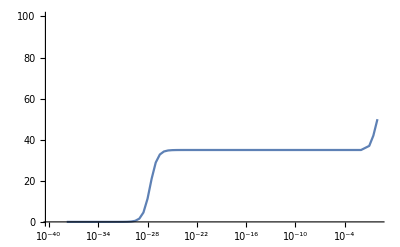

```mathematica
plotA=With[{Z=100,β=-10.,is=35},
Module[{CoI,TMat},
Monitor[data=Table[
{CoI,TMat}=TransitionMatrixESML[2,T,Z,{β,μ,is}];
Flatten@{μ,Plus@@Times@@StationaryDistributionESML[2,Z,CoI,TMat]}
,{μ,10.^FindDivisions[Log10[{10^-39,10^0}],150]}];
,μ];
];
ListLogLinearPlot[
data[[All,{1,#}]]&/@Range[2,2], Joined->True
,PlotRange->{0,Z}]
]
```

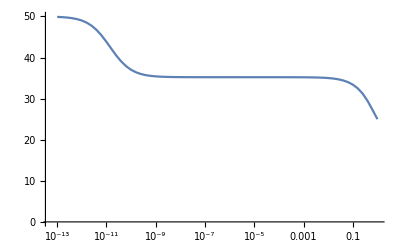

```mathematica
plotB=With[{Z=50,β=-10.,is=35},
Module[{Mat,vec},

Monitor[

data=Table[

Mat=SparseArray[{{i_,j_}/;j==i+1:>Tp[i-1,Z,is,β,μ],{i_,j_}/;j==i-1:>Tm[i-1,Z,is,β,μ],{i_,j_}/;j==i:>1-If[i<Z+1,Tp[i-1,Z,is,β,μ],0]-If[i>1,Tm[i-1,Z,is,β,μ],0]},{Z+1,Z+1}];
vec=Eigenvectors[Transpose[Mat],1,Method->{"Arnoldi", "Shift"->1.0000000001}][[1]];
vec=vec/Total[vec];
Flatten@{μ,(Plus@@Times@@{vec,Range[0,Z]})}
,{μ,10.^FindDivisions[Log10[{10^-13,10^-0}],100]}];
,μ];
ListLogLinearPlot[
data[[All,{1,#}]]&/@Range[2,2], Joined->True
,PlotRange->{0,Z}]

]
]
```

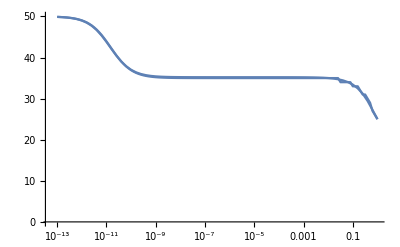

```mathematica
Show[plotA,plotB]
```